# Using the Keyboard to Enter Quantum Computing Notation in Mathematica

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx

## Introduction

This is a tutorial on the use of Quantum`Computing` Mathematica add-on to enter Quantum Computing notation (kets, gates, quantum circuits, etc) in Mathematica.

## Load the Package

First load the Quantum`Computing` package. Write:
Needs["Quantum`Computing`"];
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will load the package and it will printa a welcome message:

```mathematica
Needs["Quantum`Computing`"]
```

Quantum`Computing` Version 2.2.0. (July 2010) 
A Mathematica package for Quantum Computing in Dirac bra-ket notation and plotting of quantum circuits
by José Luis Gómez-Muñoz

Execute SetComputingAliases[] in order to use the keyboard to enter quantum objects in Dirac's notation
SetComputingAliases[] must be executed again in each new notebook that is created

In order to use the keyboard to enter quantum objects write:
SetComputingAliases[ ];
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will print a message with all the new keyboard aliases. Remember that SetComputingAliases[ ] must be evaluated again in each new notebook:

```mathematica
SetComputingAliases[]
```

ALIASES:
[ESC]on[ESC]        Quantum concatenation symbol (operator application, inner product and outer product)
[ESC]qket0[ESC]     Ket of qubit 0 template
[ESC]qbra0[ESC]     Bra of qubit 0 template
[ESC]qket1[ESC]     Ket of qubit 1 template
[ESC]qbra1[ESC]     Bra of qubit 1 template
[ESC]qket[ESC]      Ket of qubit template
[ESC]qqket[ESC]     Ket of two qubits template
[ESC]qqqket[ESC]    Ket of three qubits template
[ESC]qbra[ESC]      Bra of qubit template
[ESC]qqbra[ESC]     Bra of two qubits template
[ESC]qqqbra[ESC]    Bra of three qubits template
[ESC]toqb[ESC]      Base-10 Integer to binary qubit template
[ESC]ket[ESC]       Ket template
[ESC]bra[ESC]       Bra template
[ESC]qb[ESC]        Qubit template
[ESC]qv[ESC]        Qubit-value template
[ESC]qketbra[ESC]   Element of a one-qubit operator template
[ESC]qqketbra[ESC]  Element of a two-qubits operator template
[ESC]qqqketbra[ESC] Element of a three-qubits operator template
[ESC]k+[ESC]        Plus ket (eigenstate of the first Pauli matrix)
[ESC]b+[ESC]        Plus bra
[ESC]k-[ESC]        Minus ket (eigenstate of the first Pauli matrix)
[ESC]b-[ESC]        Minus bra
[ESC]k00[ESC]       Ket of Bell State 00
[ESC]k01[ESC]       Ket of Bell State 01
[ESC]k10[ESC]       Ket of Bell State 10
[ESC]k11[ESC]       Ket of Bell State 11
[ESC]b00[ESC]       Bra of Bell State 00
[ESC]b01[ESC]       Bra of Bell State 01
[ESC]b10[ESC]       Bra of Bell State 10
[ESC]b11[ESC]       Bra of Bell State 11
[ESC]kphi+[ESC]     Ket of Bell State phi+
[ESC]kpsi+[ESC]     Ket of Bell State psi+
[ESC]kphi-[ESC]     Ket of Bell State phi-
[ESC]kpsi-[ESC]     Ket of Bell State psi-
[ESC]bphi+[ESC]     Bra of Bell State phi+
[ESC]bpsi+[ESC]     Bra of Bell State psi+
[ESC]bphi-[ESC]     Bra of Bell State phi-
[ESC]bpsi-[ESC]     Bra of Bell State psi-
[ESC]her[ESC]       Hermitian conjugate template
[ESC]con[ESC]       Complex conjugate template
[ESC]norm[ESC]      Quantum norm template
[ESC]trace[ESC]     Partial trace template
[ESC]tp[ESC]        Tensor-product symbol
[ESC]tprod[ESC]     Tensor-product template
[ESC]tprodqb[ESC]   Tensor-product of Qubit template
[ESC]tpow[ESC]      Tensor-power template
[ESC]tpowqb[ESC]    Tensor-power of Qubit template
[ESC]s0[ESC]        0th-Pauli operator (Identity) template
[ESC]s1[ESC]        1st-Pauli operator (X) template
[ESC]s2[ESC]        2nd-Pauli operator (Y) template
[ESC]s3[ESC]        3rd-Pauli operator (Z) template
[ESC]so[ESC]        0th-Pauli operator (Identity) template
[ESC]sx[ESC]        1st-Pauli operator (X) template
[ESC]sy[ESC]        2nd-Pauli operator (Y) template
[ESC]sz[ESC]        3rd-Pauli operator (Z) template
[ESC]sp[ESC]        General Pauli operator template
[ESC]ig[ESC]        Identity gate template
[ESC]xg[ESC]        Pauli-X gate
[ESC]yg[ESC]        Pauli-Y gate
[ESC]zg[ESC]        Pauli-Z gate
[ESC]hg[ESC]        Haddamard gate
[ESC]pg[ESC]        Parametric phase gate
[ESC]sg[ESC]        S Phase gate
[ESC]tg[ESC]        T π/8 gate 
[ESC]swap[ESC]      Swap gate
[ESC]cgate[ESC]     Controlled-Gate template
[ESC]ccgate[ESC]    Controlled-controlled-Gate template
[ESC]cccgate[ESC]   Controlled-controlled-controlled-Gate template
[ESC]cnot[ESC]      Controlled-Not template
[ESC]ccnot[ESC]     Controlled-controlled-Not template
[ESC]cccnot[ESC]    Controlled-controlled-controlled-Not template
[ESC]toff[ESC]      Toffoli gate
[ESC]fred[ESC]      Fredkin gate
[ESC]qg[ESC]        Quantum gate of one argument 
[ESC]qqg[ESC]       Quantum gate of one argument applied to two qubits
[ESC]qqqg[ESC]      Quantum gate of one argument applied to three qubits
[ESC]qgg[ESC]       Quantum gate of two arguments 
[ESC]qggg[ESC]      Quantum gate of three arguments 
[ESC]pqg[ESC]       Parametric quantum gate of one argument 
[ESC]qr[ESC]        Quantum register template 
[ESC]qrg[ESC]       Quantum-register gate template 

SetComputingAliases[] must be executed again in each new notebook that is created, only one time per notebook.

## Entering Quantum Computing Notation

In order to enter a logical zero in the first qubit, press the following keys (Warning: do not type the letter O instead of the number 0. Do not type the letter I nor the letter l instead of the number 1):
[ESC]qket0[ESC]
then press the [TAB] key in order to select the place-holder □ and press:
1
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
|Subscript[0, OverHat[1]]⟩
```

|0_OverHat[1]⟩

Quantum Computing kets can be easily entered. For example, press:
[ESC]k+[ESC][TAB]3
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
|+_OverHat[3]⟩
```

|+_OverHat[3]⟩

The command QuantumEvaluate gives the representation of this ket in terms of the computational basis:

```mathematica
QuantumEvaluate[|+_OverHat[3]⟩]
```

(|0_OverHat[3]⟩)/(√2)+(|1_OverHat[3]⟩)/(√2)

In order to enter the ket of the first Bell state, press the keys:
[ESC]k00[ESC]
then press the [TAB] one or two times in order to select the first place-holder □ and press:
1[TAB]2
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
|Subscript[ℬ, 00,OverHat[1],OverHat[2]]⟩
```

|ℬ_(00,OverHat[1],OverHat[2])⟩

The command QuantumEvaluate gives the representation of this ket in terms of the computational basis:

```mathematica
QuantumEvaluate[|Subscript[ℬ, 00,OverHat[1],OverHat[2]]⟩]
```

(|0_OverHat[1],0_OverHat[2]⟩)/(√2)+(|1_OverHat[1],1_OverHat[2]⟩)/(√2)

In order to enter the ket of the first Bell state in the Phi-Psi notation, press the keys:
[ESC]kphi+[ESC]
then press the [TAB] one or two times in order to select the first place-holder □ and press:
1[TAB]2
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
|SuperPlus[Subscript[Φ, OverHat[1],OverHat[2]]]⟩
```

|Φ_(OverHat[1],OverHat[2])^+⟩

The command QuantumEvaluate gives the representation of this ket in terms of the computational basis:

```mathematica
QuantumEvaluate[|SuperPlus[Subscript[Φ, OverHat[1],OverHat[2]]]⟩]
```

(|0_OverHat[1],0_OverHat[2]⟩)/(√2)+(|1_OverHat[1],1_OverHat[2]⟩)/(√2)

In order to enter a tensor product of qubits, press the keys:
[ESC]qket0[ESC][ESC]tp[ESC][ESC]qket1[ESC]
then press the [TAB] key one or two times in order to select the first place-holder □ and press:
1[TAB]2
(Warning: Do not type the letter O instead of the number 0. Do not type the letter I nor the letter l instead of the number 1)
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
|Subscript[0, OverHat[1]]⟩⊗|Subscript[1, OverHat[2]]⟩
```

|0_OverHat[1],1_OverHat[2]⟩

In order to enter the ket of two qubits with logical zero, press the keys:
[ESC]qqket[ESC]
Then press the [TAB] key one or more times to select the first "place holder" □, and press the keys:
0[TAB]1[TAB]0[TAB]2
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩
```

|0_OverHat[1],0_OverHat[2]⟩

In order to enter an internal product, press the keys:
[ESC]qbra0[ESC][ESC]on[ESC][ESC]qket1[ESC]
Then press the [TAB] key one or more times to select the first "place holder" □, and press the keys:
4[TAB]4
(Notice that in the bra and in the ket the qubit number is the SAME)
then press at the same time the keys ⇧-⌤ to evaluate.
The relative position of the bras, kets and operators determines without any ambiguity if [ESC]on[ESC] is an internal product, an external product or an operator application.

```mathematica
⟨Subscript[0, OverHat[4]]|·|Subscript[1, OverHat[4]]⟩
```

0

We can obtain specific information for Quantum Mathematica commands. For example, write:
? QuantumEvaluate
then press at the same time the keys ⇧-⌤

```mathematica
?QuantumEvaluate
```

QuantumEvaluate[expr] gives Dirac Kets and Bras for expr.
Notice that expr is made of quantum gates connected by the quantum product ·
 In order to enter the quantum product · execute SetComputingAliases[]. Then press:
[ESC]on[ESC]        Quantum product template
SetComputingAliases[] must be executed again in each new notebook that is created, only one time per notebook.

Here we obtain a matrix element of the Hadamard-Gate operator:
QuantumEvaluate[ [ESC]qbra1[ESC][ESC]on[ESC][ESC]hg[ESC][ESC]on[ESC][ESC]qket1[ESC] ]
Then press the [TAB] key one or more times to select the first "place holder" □, and press the keys:
1[TAB]1[TAB]1
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
QuantumEvaluate[⟨Subscript[1, OverHat[1]]|·Subscript[ℋ, OverHat[1]]·|Subscript[1, OverHat[1]]⟩]
```

-1/(√2)

Here we can see the matrix that corresponds to the Hadamard-Gate.

```mathematica
QuantumMatrixForm[Subscript[ℋ, OverHat[1]]]
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

QuantumMatrixForm[] and QuantumTensorForm[] give an output that is adequate for displaying purposes. On the other hand, for calculation purposes, is better to use QuantumMatrix[] and QuantumTensor[], which give a standard Mathematica matrix (list) as an output:

```mathematica
QuantumMatrix[Subscript[ℋ, OverHat[1]]]
```

{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}

The Pauli gates can be entered:
QuantumEvaluate[ [ESC]yg[ESC] ] [TAB]3
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
QuantumEvaluate[Subscript[𝒴, OverHat[3]]]
```

ⅈ |1_OverHat[3]⟩·⟨0_OverHat[3]|-ⅈ |0_OverHat[3]⟩·⟨1_OverHat[3]|

This is the tensor form of the operator. Notice that it is assumed that there is only one qubit, eventhogh the label of that qubit is "3". Below it is explained how to indicate that more qubits also exist:

```mathematica
QuantumTensorForm[Subscript[𝒴, OverHat[3]]]
```

(0 | -ⅈ
ⅈ | 0)

Here we use identity gates to obtain a tensor form of the operator acting on the third qubit, taking into account that the first and second qubits also exist.
QuantumTensorForm[ [ESC]ig[ESC] [ESC]tp[ESC] [ESC]ig[ESC] [ESC]tp[ESC] [ESC]yg[ESC] ]
Then press the [TAB] key several times to select the first "place holder" □, and press the keys:
 1 [TAB]2 [TAB]3
then press at the same time the keys ⇧-⌤ to evaluate.
(NOTE: The template [ESC]tp[ESC] and the template [ESC]on[ESC] give exactly the same result in any calculation. Both of them mean internal product, external product, operator application, etc. Their precise meaning is given without ambiguity by the objects before and after them. So you can use [ESC]on[ESC] instead of [ESC]tp[ESC] and viceversa in any calculation)

```mathematica
QuantumTensorForm[Subscript[ℐ, OverHat[1]]⊗Subscript[ℐ, OverHat[2]]⊗Subscript[𝒴, OverHat[3]]]
```

(((0 | -ⅈ
ⅈ | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | -ⅈ
ⅈ | 0)) | ((0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0))
((0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0)) | ((0 | -ⅈ
ⅈ | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | -ⅈ
ⅈ | 0)))

Another way to specify that qubits OverHat[1] and OverHat[2] exist is using the option QubitList. The arrow → can be entered pressing the keys [ESC]->[ESC]

```mathematica
QuantumTensorForm[Subscript[𝒴, OverHat[3]],QubitList->{1,2,3}]
```

(((0 | -ⅈ
ⅈ | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | -ⅈ
ⅈ | 0)) | ((0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0))
((0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0)) | ((0 | -ⅈ
ⅈ | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | -ⅈ
ⅈ | 0)))

In order to print the Truth table for an operator, press the keys: 
QuantumTableForm[ [ESC]cnot[ESC][ESC]on[ESC][ESC]hg[ESC] ]
Then press the [TAB] key several times to select the first "place holder" □, and press the keys:
a[TAB]b[TAB]a
then press at the same time the keys ⇧-⌤ to evaluate.
(NOTE: The template [ESC]tp[ESC] and the template [ESC]on[ESC] give exactly the same result in any calculation. Both of them mean internal product, external product, operator application, etc. Their precise meaning is given without ambiguity by the objects before and after them. So you can use [ESC]on[ESC] instead of [ESC]tp[ESC] and viceversa in any calculation)

```mathematica
QuantumTableForm[(𝒞^{â})[Subscript[𝒩𝒪𝒯, b̂]]·Subscript[ℋ, â]]
```

|   Input |   Output
0 | |0_(â),0_(b̂)⟩ | (|0_(â),0_(b̂)⟩)/(√2)+(|1_(â),1_(b̂)⟩)/(√2)
1 | |0_(â),1_(b̂)⟩ | (|0_(â),1_(b̂)⟩)/(√2)+(|1_(â),0_(b̂)⟩)/(√2)
2 | |1_(â),0_(b̂)⟩ | (|0_(â),0_(b̂)⟩)/(√2)-(|1_(â),1_(b̂)⟩)/(√2)
3 | |1_(â),1_(b̂)⟩ | (|0_(â),1_(b̂)⟩)/(√2)-(|1_(â),0_(b̂)⟩)/(√2)

The TraditionalForm representation is closer to the notation used in textbooks and papers:

```mathematica
TraditionalForm[QuantumTableForm[ (𝒞^{â})[Subscript[𝒩𝒪𝒯, b̂]]·Subscript[ℋ, â]]]
```

|   Input |   Output
0 | |00⟩ | (|00⟩)/(√2)+(|11⟩)/(√2)
1 | |01⟩ | (|01⟩)/(√2)+(|10⟩)/(√2)
2 | |10⟩ | (|00⟩)/(√2)-(|11⟩)/(√2)
3 | |11⟩ | (|01⟩)/(√2)-(|10⟩)/(√2)

In order to obtain the operator in Dirac notation, press the keys:
QuantumEvaluate[ [ESC]cnot[ESC][ESC]on[ESC][ESC]hg[ESC] ]
Then press the [TAB] key several times to select the first "place holder" □, and press the keys:
a[TAB]b[TAB]a
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
QuantumEvaluate[(𝒞^{â})[Subscript[𝒩𝒪𝒯, b̂]]·Subscript[ℋ, â]]
```

(|0_(â),0_(b̂)⟩·⟨0_(â),0_(b̂)|)/(√2)+(|1_(â),1_(b̂)⟩·⟨0_(â),0_(b̂)|)/(√2)+(|0_(â),1_(b̂)⟩·⟨0_(â),1_(b̂)|)/(√2)+(|1_(â),0_(b̂)⟩·⟨0_(â),1_(b̂)|)/(√2)+(|0_(â),0_(b̂)⟩·⟨1_(â),0_(b̂)|)/(√2)-(|1_(â),1_(b̂)⟩·⟨1_(â),0_(b̂)|)/(√2)+(|0_(â),1_(b̂)⟩·⟨1_(â),1_(b̂)|)/(√2)-(|1_(â),0_(b̂)⟩·⟨1_(â),1_(b̂)|)/(√2)

The TraditionalForm representation is closer to the notation used in textbooks and papers:

```mathematica
TraditionalForm[QuantumEvaluate[(𝒞^{â})[Subscript[𝒩𝒪𝒯, b̂]]·Subscript[ℋ, â]]]
```

(|00⟩⟨00|)/(√2)+(|11⟩⟨00|)/(√2)+(|01⟩⟨01|)/(√2)+(|10⟩⟨01|)/(√2)+(|00⟩⟨10|)/(√2)-(|11⟩⟨10|)/(√2)+(|01⟩⟨11|)/(√2)-(|10⟩⟨11|)/(√2)

TeXForm produces a TEX output that can be copy-pasted to a TEX editor:

```mathematica
TeXForm[TraditionalForm[QuantumEvaluate[(𝒞^{â})[𝒩𝒪𝒯[b̂]]·ℋ[â]]]]
```

\frac{|00\rangle \langle 00|}{\sqrt{2}}+\frac{|11\rangle \langle
   00|}{\sqrt{2}}+\frac{|01\rangle \langle
   01|}{\sqrt{2}}+\frac{|10\rangle \langle
   01|}{\sqrt{2}}+\frac{|00\rangle \langle
   10|}{\sqrt{2}}-\frac{|11\rangle \langle
   10|}{\sqrt{2}}+\frac{|01\rangle \langle
   11|}{\sqrt{2}}-\frac{|10\rangle \langle 11|}{\sqrt{2}}

In order to obtain the operator in Pauli operators, press the keys:
PauliExpand[ [ESC]cnot[ESC][ESC]on[ESC][ESC]hg[ESC] ]
Then press the [TAB] key several times to select the first "place holder" □, and press the keys:
a[TAB]b[TAB]a
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
PauliExpand[(𝒞^{â})[Subscript[𝒩𝒪𝒯, b̂]]·Subscript[ℋ, â]]
```

(σ_(0,â)·σ_(0,b̂))/(2 √2)+(σ_(𝒳,â)·σ_(0,b̂))/(2 √2)+(ⅈ σ_(𝒴,â)·σ_(0,b̂))/(2 √2)+(σ_(𝒵,â)·σ_(0,b̂))/(2 √2)-(σ_(0,â)·σ_(𝒳,b̂))/(2 √2)+(σ_(𝒳,â)·σ_(𝒳,b̂))/(2 √2)-(ⅈ σ_(𝒴,â)·σ_(𝒳,b̂))/(2 √2)+(σ_(𝒵,â)·σ_(𝒳,b̂))/(2 √2)

The TraditionalForm representation is closer to the notation used in textbooks and papers:

```mathematica
TraditionalForm[PauliExpand[(𝒞^{â})[Subscript[𝒩𝒪𝒯, b̂]]·Subscript[ℋ, â]]]
```

-(ⅈ σ_a^𝒴σ_b^𝒳)/(2 √2)+(σ_a^𝒵σ_b^𝒳)/(2 √2)+(σ_a^𝒳σ_b^0)/(2 √2)-(σ_a^0σ_b^𝒳)/(2 √2)+(σ_a^𝒳σ_b^𝒳)/(2 √2)+(ⅈ σ_a^𝒴σ_b^0)/(2 √2)+(σ_a^𝒵σ_b^0)/(2 √2)+(σ_a^0σ_b^0)/(2 √2)

TeXForm produces a TEX output that can be copy-pasted to a TEX editor:

```mathematica
TeXForm[TraditionalForm[PauliExpand[(𝒞^{â})[Subscript[𝒩𝒪𝒯, b̂]]·Subscript[ℋ, â]]]]
```

-\frac{i \sigma _a^{\mathcal{Y}}\sigma _b^{\mathcal{X}}}{2
   \sqrt{2}}+\frac{\sigma _a^{\mathcal{Z}}\sigma
   _b^{\mathcal{X}}}{2 \sqrt{2}}+\frac{\sigma
   _a^{\mathcal{X}}\sigma _b^{\mathit{0}}}{2
   \sqrt{2}}-\frac{\sigma _a^{\mathit{0}}\sigma
   _b^{\mathcal{X}}}{2 \sqrt{2}}+\frac{\sigma
   _a^{\mathcal{X}}\sigma _b^{\mathcal{X}}}{2 \sqrt{2}}+\frac{i
   \sigma _a^{\mathcal{Y}}\sigma _b^{\mathit{0}}}{2
   \sqrt{2}}+\frac{\sigma _a^{\mathcal{Z}}\sigma
   _b^{\mathit{0}}}{2 \sqrt{2}}+\frac{\sigma _a^{\mathit{0}}\sigma
   _b^{\mathit{0}}}{2 \sqrt{2}}

In order to see the circuit operator in Tensor notation, press the keys:
QuantumTensorForm[ [ESC]cnot[ESC][ESC]on[ESC][ESC]hg[ESC] ]
Then press the [TAB] key several times to select the first "place holder" □, and press the keys:
a[TAB]b[TAB]a
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
QuantumTensorForm[(𝒞^{â})[Subscript[𝒩𝒪𝒯, b̂]]·Subscript[ℋ, â]]
```

((1/(√2) | 0
0 | 1/(√2)) | (1/(√2) | 0
0 | 1/(√2))
(0 | 1/(√2)
1/(√2) | 0) | (0 | -1/(√2)
-1/(√2) | 0))

Remember that for actual Mathematica calculations QuantumTensor[] must be used instead of QuantumTensorForm[]:

```mathematica
QuantumTensor[(𝒞^{â})[Subscript[𝒩𝒪𝒯, b̂]]·Subscript[ℋ, â]]
```

{{{{1/(√2),0},{0,1/(√2)}},{{1/(√2),0},{0,1/(√2)}}},{{{0,1/(√2)},{1/(√2),0}},{{0,-1/(√2)},{-1/(√2),0}}}}

In order to see the circuit operator in Matrix notation, press the keys:
QuantumMatrixForm[ [ESC]cnot[ESC][ESC]on[ESC][ESC]hg[ESC] ]
Then press the [TAB] key several times to select the first "place holder" □, and press the keys:
a[TAB]b[TAB]a
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
QuantumMatrixForm[(𝒞^{â})[Subscript[𝒩𝒪𝒯, b̂]]·Subscript[ℋ, â]]
```

(1/(√2) | 0 | 1/(√2) | 0
0 | 1/(√2) | 0 | 1/(√2)
0 | 1/(√2) | 0 | -1/(√2)
1/(√2) | 0 | -1/(√2) | 0)

Remember that for actual Mathematica calculations QuantumMatrix[] must be used instead of QuantumMatrixForm[]:

```mathematica
QuantumMatrix[(𝒞^{â})[Subscript[𝒩𝒪𝒯, b̂]]·Subscript[ℋ, â]]
```

{{1/(√2),0,1/(√2),0},{0,1/(√2),0,1/(√2)},{0,1/(√2),0,-1/(√2)},{1/(√2),0,-1/(√2),0}}

In order to generate a Bell state from a state of two qubits with logical zero, press the keys:
QuantumEvaluate[ [ESC]cnot[ESC][ESC]on[ESC][ESC]hg[ESC][ESC]on[ESC][ESC]qqket[ESC] ]
Then press the [TAB] key several times to select the first "place holder" □, and press the keys:
1[TAB]2[TAB]1[TAB]0[TAB]1[TAB]0[TAB]2
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
QuantumEvaluate[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]·|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩]
```

(|0_OverHat[1],0_OverHat[2]⟩)/(√2)+(|1_OverHat[1],1_OverHat[2]⟩)/(√2)

In order to plot the quantum circuit, press the keys:
QuantumPlot[ [ESC]cnot[ESC][ESC]on[ESC][ESC]hg[ESC][ESC]on[ESC][ESC]qqket[ESC] ]
Then press the [TAB] key several times to select the first "place holder" □, and press the keys:
1[TAB]2[TAB]1[TAB]0[TAB]1[TAB]0[TAB]2
then press at the same time the keys ⇧-⌤ to evaluate:

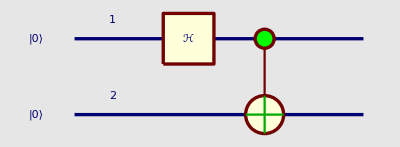

```mathematica
QuantumPlot[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]·|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩]
```

In order to plot in 3D the quantum circuit, press the keys:
QuantumPlot3D[ [ESC]cnot[ESC][ESC]on[ESC][ESC]hg[ESC][ESC]on[ESC][ESC]qqket[ESC] ]
Then press the [TAB] key several times to select the first "place holder" □, and press the keys:
1[TAB]2[TAB]1[TAB]0[TAB]1[TAB]0[TAB]2
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
QuantumPlot3D[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]·|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩]
```

-Graphics3D-

In order to enter the tensor product of a quantum expression, press the keys:
[ESC]tprod[ESC]
Then press the [TAB] key one or more times to select the first "place holder" □, and press the keys:
j[TAB]1[TAB]3[TAB]
Then press the keys:
[ESC]cnot[ESC]
Then press the [TAB] key one or more times to select the first "place holder" □, and press the keys:
j [TAB] j+1
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
⊗_(j=1)^3(𝒞^{ĵ})[Subscript[𝒩𝒪𝒯, OverHat[j+1]]]
```

𝒞^{OverHat[1]}[𝒩𝒪𝒯_OverHat[2]]·𝒞^{OverHat[2]}[𝒩𝒪𝒯_OverHat[3]]·𝒞^{OverHat[3]}[𝒩𝒪𝒯_OverHat[4]]

In order to plot the circuit of a tensor product of a quantum expression, press the keys:
QuantumPlot[ [ESC]tprod[ESC] ]
Then press the [TAB] key one or more times to select the first "place holder" □, and press the keys:
j[TAB]1[TAB]3[TAB]
Then press the keys:
[ESC]cnot[ESC]
Then press the [TAB] key one or more times to select the first "place holder" □, and press the keys:
j [TAB] j+1
then press at the same time the keys ⇧-⌤ to evaluate:

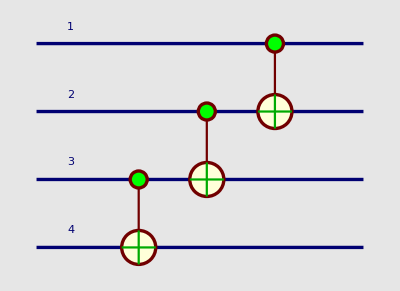

```mathematica
QuantumPlot[⊗_(j=1)^3(𝒞^{ĵ})[Subscript[𝒩𝒪𝒯, OverHat[j+1]]]]
```

In order to plot in 3D the circuit of a tensor product of a quantum expression, press the keys:
QuantumPlot3D[ [ESC]tprod[ESC] ]
Then press the [TAB] key one or more times to select the first "place holder" □, and press the keys:
j[TAB]1[TAB]3[TAB]
Then press the keys:
[ESC]cnot[ESC]
Then press the [TAB] key one or more times to select the first "place holder" □, and press the keys:
j [TAB] j+1
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
QuantumPlot3D[⊗_(j=1)^3(𝒞^{ĵ})[Subscript[𝒩𝒪𝒯, OverHat[j+1]]]]
```

-Graphics3D-

The same tensor product can be entered as a "tensor power". Press the keys:
QuantumPlot[ [ESC]tpow[ESC] ]
Then press the [TAB] key one or more times to select the first "place holder" □, and press the keys:
[ESC]cnot[ESC]
Then press the [TAB] key one or more times to select the first "place holder" □, and press the keys:
1[TAB]2[TAB]3
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
QuantumPlot[((𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]])^(⊗3)]
```

-Graphics-

On the other hand, a "normal power" is very different from a "tensor power". Press the keys:
QuantumPlot[ [ESC]po[ESC] , QuantumGatePowers[ESC]->[ESC]False ]
Then press the [TAB] key one or more times to select the first "place holder" □, and press the keys:
[ESC]cnot[ESC]
Then press the [TAB] key one or more times to select the first "place holder" □, and press the keys:
1[TAB]2[TAB]3
then press at the same time the keys ⇧-⌤ to evaluate:

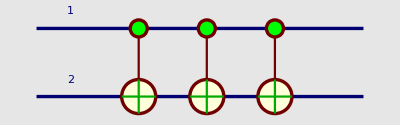

```mathematica
QuantumPlot[((𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]])^3,QuantumGatePowers->False]
```

This is a more elaborated circuit. Notice how the syntaxis indicates if a gate is before or after the measuring meters. Press [ESC]cgate[ESC] for the controlled-gate template 𝒞^{OverHat[□]}[□]; [ESC]cnot[ESC] for the control-not template 𝒞^{OverHat[□]}[𝒩𝒪𝒯[OverHat[□]]]; [ESC]xg[ESC] for the 𝒳[OverHat[□]] template, etc.

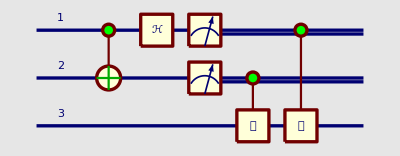

```mathematica
QuantumPlot[(𝒞^{OverHat[1]})[Subscript[𝒵, OverHat[3]]]·(𝒞^{OverHat[2]})[Subscript[𝒳, OverHat[3]]]·QubitMeasurement[Subscript[ℋ, OverHat[1]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]],{OverHat[1],OverHat[2]}]]
```

Plot of the same circuit, now applied to the initial ket |ℬ_(00,OverHat[2],OverHat[3])⟩⊗(a|0_OverHat[1]⟩+b|1_OverHat[1]⟩)

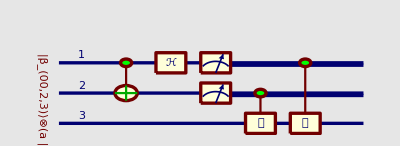

```mathematica
QuantumPlot[(𝒞^{OverHat[1]})[Subscript[𝒵, OverHat[3]]]·(𝒞^{OverHat[2]})[Subscript[𝒳, OverHat[3]]]·QubitMeasurement[Subscript[ℋ, OverHat[1]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·|Subscript[ℬ, 00,OverHat[2],OverHat[3]]⟩⊗(a|Subscript[0, OverHat[1]]⟩+b|Subscript[1, OverHat[1]]⟩),{OverHat[1],OverHat[2]}]]
```

Evaluation of the same circuit, applied to the initial ket |ℬ_(00,OverHat[2],OverHat[3])⟩⊗(a|0_OverHat[1]⟩+b|1_OverHat[1]⟩). Notice that all possible outputs have the 3rd qubit in the combination a |0_OverHat[3]⟩+b |1_OverHat[3]⟩, therefore this circuit "teleports" (cuts and pastes) the initial state from qubit OverHat[1] (which initially is a|0_OverHat[1]⟩+b|1_OverHat[1]⟩) to the qubit OverHat[3] (which finally becomes a |0_OverHat[3]⟩+b |1_OverHat[3]⟩)

```mathematica
QuantumEvaluate[(𝒞^{OverHat[1]})[Subscript[𝒵, OverHat[3]]]·(𝒞^{OverHat[2]})[Subscript[𝒳, OverHat[3]]]·QubitMeasurement[Subscript[ℋ, OverHat[1]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·|Subscript[ℬ, 00,OverHat[2],OverHat[3]]⟩⊗(a|Subscript[0, OverHat[1]]⟩+b|Subscript[1, OverHat[1]]⟩),{OverHat[1],OverHat[2]}]]
```

Probability | Measurement | State
1/4 | {{0_OverHat[1],0_OverHat[2]}} | |0_OverHat[1]⟩⊗|0_OverHat[2]⟩⊗((a |0_OverHat[3]⟩)/(√(a a^*+b b^*))+(b |1_OverHat[3]⟩)/(√(a a^*+b b^*)))
1/4 | {{0_OverHat[1],1_OverHat[2]}} | |0_OverHat[1]⟩⊗|1_OverHat[2]⟩⊗((a |0_OverHat[3]⟩)/(√(a a^*+b b^*))+(b |1_OverHat[3]⟩)/(√(a a^*+b b^*)))
1/4 | {{1_OverHat[1],0_OverHat[2]}} | |1_OverHat[1]⟩⊗|0_OverHat[2]⟩⊗((a |0_OverHat[3]⟩)/(√(a a^*+b b^*))+(b |1_OverHat[3]⟩)/(√(a a^*+b b^*)))
1/4 | {{1_OverHat[1],1_OverHat[2]}} | |1_OverHat[1]⟩⊗|1_OverHat[2]⟩⊗((a |0_OverHat[3]⟩)/(√(a a^*+b b^*))+(b |1_OverHat[3]⟩)/(√(a a^*+b b^*)))
Probability | Measurement | State

In order to represent a 9 as a binary number made of 5 qubits, press the keys:
[ESC]toqb[ESC] [TAB] 9  [TAB] 5
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
(|9⟩)_5
```

|0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4],1_OverHat[5]⟩

This is a normalized, equally-weighted, linear combination of the computational basis kets for three qubits. Press [ESC]si[ESC] for the sigma notation template ∑_□^□ □

```mathematica
1/(√8)∑_(j=0)^7 (|j⟩)_3
```

1/(2 √2)(|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩+|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩+|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩+|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩+|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩+|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩+|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩+|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)

Here we calculate the norm. Press [ESC]norm[ESC] for the norm template ‖□‖

```mathematica
‖1/(√8)∑_(j=0)^7 (|j⟩)_3‖
```

1

This is a normalized, equally-weighted, linear combination of the computational basis kets for four qubits:

```mathematica
n=2^4;
1/(√n)∑_(j=0)^(n-1) (|j⟩)_Log[2,n]
```

1/4 (|0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+|0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+|0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+|0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+|0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+|0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+|0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+|0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+|1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+|1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+|1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+|1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+|1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+|1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+|1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+|1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩)

In order to save the definition of a ket, press the keys:
[ESC]ket[ESC] = a [ESC]qket[ESC] +b [ESC]qket[ESC]
Then press the [TAB] key one or more times to select the first "place holder" □, and press the keys:
[ESC]psi[ESC][TAB]0[TAB]1[TAB]1[TAB]1
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
|ψ⟩=a|Subscript[0, OverHat[1]]⟩+b|Subscript[1, OverHat[1]]⟩
```

a |0_OverHat[1]⟩+b |1_OverHat[1]⟩

The correspondig bra can be used:
[ESC]bra[ESC] [TAB] [ESC]psi[ESC]
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
⟨ψ|
```

a^* ⟨0_OverHat[1]|+b^* ⟨1_OverHat[1]|

An external product can be calculated from the ket that was defined. Press the keys:
Expand[ [ESC]ket[ESC] [ESC]on[ESC] [ESC]bra[ESC]  ]
then press the keys:
[TAB] [ESC]psi[ESC] [TAB] [ESC]psi[ESC]
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
Expand[|ψ⟩·⟨ψ|]
```

a a^* |0_OverHat[1]⟩·⟨0_OverHat[1]|+b a^* |1_OverHat[1]⟩·⟨0_OverHat[1]|+a b^* |0_OverHat[1]⟩·⟨1_OverHat[1]|+b b^* |1_OverHat[1]⟩·⟨1_OverHat[1]|

An internal product can be calculated from the ket that was defined. Press the keys:
[ESC]bra[ESC] [ESC]on[ESC] [ESC]ket[ESC] [TAB] [ESC]psi[ESC] [TAB] [ESC]psi[ESC]
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
⟨ψ|·|ψ⟩
```

a a^*+b b^*

The norm of a quantum expression can be calculated. Press the keys:
[ESC]norm[ESC] [TAB] [ESC]ket[ESC] [TAB] [ESC]psi[ESC]
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
‖|ψ⟩‖
```

√(a a^*+b b^*)

Advanced Mathematica technical info: The definition is stored as an "upvalue" of psi ψ
 ? [ESC]psi[ESC]
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
?ψ
```

Global`ψ

|ψ⟩^=a |0_OverHat[1]⟩+b |1_OverHat[1]⟩

In order to save the definition of another ket, press the keys:
[ESC]ket[ESC] = x [ESC]qket[ESC] +y [ESC]qket[ESC]
Then press the [TAB] key one or more times to select the first "place holder" □, and press the keys:
[ESC]x[ESC][TAB]0[TAB]1[TAB]1[TAB]1
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
|ξ⟩=x|Subscript[0, OverHat[1]]⟩+y|Subscript[1, OverHat[1]]⟩
```

x |0_OverHat[1]⟩+y |1_OverHat[1]⟩

Different operations can  be performed on the kets that were defined, and the results (output) of those operations are valid Mathematica expressions that can be copy-pasted and used as part of Mathematica input in other commands:

```mathematica
⟨ξ|·|ψ⟩
```

a x^*+b y^*

Different operations can  be performed on the kets that were defined, and the results (output) of those operations are valid Mathematica expressions that can be copy-pasted and used as part of Mathematica input in other commands:

```mathematica
Expand[|ξ⟩·⟨ψ|]
```

x a^* |0_OverHat[1]⟩·⟨0_OverHat[1]|+y a^* |1_OverHat[1]⟩·⟨0_OverHat[1]|+x b^* |0_OverHat[1]⟩·⟨1_OverHat[1]|+y b^* |1_OverHat[1]⟩·⟨1_OverHat[1]|

A "Power" can be entered pressing [ESC]po[ESC]

```mathematica
Expand[(|ξ⟩·⟨ψ|)^2]
```

x^2 (a^*)^2 |0_OverHat[1]⟩·⟨0_OverHat[1]|+x y a^* b^* |0_OverHat[1]⟩·⟨0_OverHat[1]|+x y (a^*)^2 |1_OverHat[1]⟩·⟨0_OverHat[1]|+y^2 a^* b^* |1_OverHat[1]⟩·⟨0_OverHat[1]|+x^2 a^* b^* |0_OverHat[1]⟩·⟨1_OverHat[1]|+x y (b^*)^2 |0_OverHat[1]⟩·⟨1_OverHat[1]|+x y a^* b^* |1_OverHat[1]⟩·⟨1_OverHat[1]|+y^2 (b^*)^2 |1_OverHat[1]⟩·⟨1_OverHat[1]|

A "Tensor Power" (□)^(⊗□) is very different from a "Power" (□)^□
In a TensorPower, the same expression is evaluated at different qubits 
The "Tensor Power" can be entered by pressing [ESC]tpow[ESC]

```mathematica
Expand[(|ξ⟩·⟨ψ|)^(⊗2)]
```

x^2 (a^*)^2 |0_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+x y (a^*)^2 |0_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+x y (a^*)^2 |1_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+y^2 (a^*)^2 |1_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+x^2 a^* b^* |0_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+x y a^* b^* |0_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+x y a^* b^* |1_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+y^2 a^* b^* |1_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+x^2 a^* b^* |0_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+x y a^* b^* |0_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+x y a^* b^* |1_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+y^2 a^* b^* |1_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+x^2 (b^*)^2 |0_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|+x y (b^*)^2 |0_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|+x y (b^*)^2 |1_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|+y^2 (b^*)^2 |1_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|

Partial trace template: [ESC]trace[ESC]
Tensor power template: [ESC]tpow[ESC]

```mathematica
Subscript[Tr, OverHat[2]][(|ξ⟩·⟨ψ|)^(⊗2)]
```

x (x (a^*)^2 |0_OverHat[1]⟩·⟨0_OverHat[1]|+y (a^*)^2 |1_OverHat[1]⟩·⟨0_OverHat[1]|+x a^* b^* |0_OverHat[1]⟩·⟨1_OverHat[1]|+y a^* b^* |1_OverHat[1]⟩·⟨1_OverHat[1]|)+y (x a^* b^* |0_OverHat[1]⟩·⟨0_OverHat[1]|+y a^* b^* |1_OverHat[1]⟩·⟨0_OverHat[1]|+x (b^*)^2 |0_OverHat[1]⟩·⟨1_OverHat[1]|+y (b^*)^2 |1_OverHat[1]⟩·⟨1_OverHat[1]|)

Partial trace template: [ESC]trace[ESC]
Tensor power template: [ESC]tpow[ESC]

```mathematica
Expand[Subscript[Tr, OverHat[2]][(|ξ⟩·⟨ψ|)^(⊗2)]]
```

x^2 (a^*)^2 |0_OverHat[1]⟩·⟨0_OverHat[1]|+x y a^* b^* |0_OverHat[1]⟩·⟨0_OverHat[1]|+x y (a^*)^2 |1_OverHat[1]⟩·⟨0_OverHat[1]|+y^2 a^* b^* |1_OverHat[1]⟩·⟨0_OverHat[1]|+x^2 a^* b^* |0_OverHat[1]⟩·⟨1_OverHat[1]|+x y (b^*)^2 |0_OverHat[1]⟩·⟨1_OverHat[1]|+x y a^* b^* |1_OverHat[1]⟩·⟨1_OverHat[1]|+y^2 (b^*)^2 |1_OverHat[1]⟩·⟨1_OverHat[1]|

Partial trace template: [ESC]trace[ESC]
Tensor power template: [ESC]tpow[ESC]

```mathematica
TraditionalForm[Expand[Subscript[Tr, OverHat[2]][(|ξ⟩·⟨ψ|)^(⊗2)]]]
```

x^2 Conjugate[a] Conjugate[b] |0⟩⟨1|+x y Conjugate[a] Conjugate[b] |0⟩⟨0|+x y Conjugate[a] Conjugate[b] |1⟩⟨1|+y^2 Conjugate[a] Conjugate[b] |1⟩⟨0|+x^2 (Conjugate[a])^2 |0⟩⟨0|+x y (Conjugate[a])^2 |1⟩⟨0|+x y (Conjugate[b])^2 |0⟩⟨1|+y^2 (Conjugate[b])^2 |1⟩⟨1|

Partial trace template: [ESC]trace[ESC]
Tensor power template: [ESC]tpow[ESC]

```mathematica
Subscript[Tr, OverHat[2]][(|ξ⟩·⟨ψ|)^(⊗2)]·|Subscript[0, OverHat[1]],Subscript[0, OverHat[3]]⟩
```

x (x (a^*)^2 |0_OverHat[1],0_OverHat[3]⟩+y (a^*)^2 |1_OverHat[1],0_OverHat[3]⟩)+y (x a^* b^* |0_OverHat[1],0_OverHat[3]⟩+y a^* b^* |1_OverHat[1],0_OverHat[3]⟩)

The standard Mathematica command Simplify[] can be used:

```mathematica
Simplify[Subscript[Tr, OverHat[2]][(|ξ⟩·⟨ψ|)^(⊗2)]·|Subscript[0, OverHat[1]],Subscript[0, OverHat[3]]⟩]
```

a^* (x a^*+y b^*) (x |0_OverHat[1],0_OverHat[3]⟩+y |1_OverHat[1],0_OverHat[3]⟩)

Press [ESC]her[ESC] for the Hermitian conjugate template (□)^†

```mathematica
(|ψ⟩)^†
```

a^* ⟨0_OverHat[1]|+b^* ⟨1_OverHat[1]|

Press [ESC]her[ESC] for the Hermitian conjugate template (□)^† and [ESC]tg[ESC] for the 𝒯_OverHat[□] template

```mathematica
SuperDagger[(Subscript[𝒯, OverHat[1]])]
```

𝒯_OverHat[1]^†

Press [ESC]her[ESC] for the Hermitian conjugate template (□)^† and [ESC]tg[ESC] for the 𝒯_OverHat[□] template

```mathematica
PauliExpand[SuperDagger[(Subscript[𝒯, OverHat[1]])]]
```

1/4 (2+(1-ⅈ) √2) σ_(0,OverHat[1])+1/4 (2-(1-ⅈ) √2) σ_(𝒵,OverHat[1])

TraditionalForm:

```mathematica
TraditionalForm[PauliExpand[SuperDagger[(Subscript[𝒯, OverHat[1]])]]]
```

1/4 (2-(1-ⅈ) √2) σ_1^𝒵+1/4 (2+(1-ⅈ) √2) σ_1^0

Press [ESC]qqft[ESC] for the template of the two-qubits Quantum Fourier Transform 𝒬ℱ𝒯_(OverHat[□],OverHat[□])

```mathematica
QuantumTableForm[Subscript[𝒬ℱ𝒯, OverHat[1],OverHat[2]]]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[2]⟩ | 0.5 |0_OverHat[1],0_OverHat[2]⟩+0.5 |0_OverHat[1],1_OverHat[2]⟩+0.5 |1_OverHat[1],0_OverHat[2]⟩+0.5 |1_OverHat[1],1_OverHat[2]⟩
1 | |0_OverHat[1],1_OverHat[2]⟩ | 0.5 |0_OverHat[1],0_OverHat[2]⟩+0.5 ⅈ |0_OverHat[1],1_OverHat[2]⟩-0.5 |1_OverHat[1],0_OverHat[2]⟩-0.5 ⅈ |1_OverHat[1],1_OverHat[2]⟩
2 | |1_OverHat[1],0_OverHat[2]⟩ | 0.5 |0_OverHat[1],0_OverHat[2]⟩-0.5 |0_OverHat[1],1_OverHat[2]⟩+0.5 |1_OverHat[1],0_OverHat[2]⟩-0.5 |1_OverHat[1],1_OverHat[2]⟩
3 | |1_OverHat[1],1_OverHat[2]⟩ | 0.5 |0_OverHat[1],0_OverHat[2]⟩-0.5 ⅈ |0_OverHat[1],1_OverHat[2]⟩-0.5 |1_OverHat[1],0_OverHat[2]⟩+0.5 ⅈ |1_OverHat[1],1_OverHat[2]⟩

Press [ESC]qqqft[ESC] for the template of the three-qubits Quantum Fourier Transform 𝒬ℱ𝒯_(OverHat[□],OverHat[□],OverHat[□])

```mathematica
QuantumEvaluate[Subscript[𝒬ℱ𝒯, â,b̂,ĉ]·|Subscript[1, â],Subscript[0, b̂],Subscript[1, ĉ]⟩]
```

0.353553 |0_(â),0_(b̂),0_(ĉ)⟩-(0.25+0.25 ⅈ) |0_(â),0_(b̂),1_(ĉ)⟩+0.353553 ⅈ |0_(â),1_(b̂),0_(ĉ)⟩+(0.25-0.25 ⅈ) |0_(â),1_(b̂),1_(ĉ)⟩-0.353553 |1_(â),0_(b̂),0_(ĉ)⟩+(0.25+0.25 ⅈ) |1_(â),0_(b̂),1_(ĉ)⟩-0.353553 ⅈ |1_(â),1_(b̂),0_(ĉ)⟩-(0.25-0.25 ⅈ) |1_(â),1_(b̂),1_(ĉ)⟩

Press [ESC]qqqft[ESC] for the template of the three-qubits Quantum Fourier Transform 𝒬ℱ𝒯_(OverHat[□],OverHat[□],OverHat[□])
Scroll to the right in order to see the complete answer

```mathematica
TraditionalForm[QuantumTableForm[Subscript[𝒬ℱ𝒯, â,b̂,ĉ]]]
```

|   Input |   Output
0 | |000⟩ | 0.353553 |000⟩+0.353553 |001⟩+0.353553 |010⟩+0.353553 |011⟩+0.353553 |100⟩+0.353553 |101⟩+0.353553 |110⟩+0.353553 |111⟩
1 | |001⟩ | 0.353553 |000⟩+(0.25+0.25 ⅈ) |001⟩+0.353553 ⅈ |010⟩-(0.25-0.25 ⅈ) |011⟩-0.353553 |100⟩-(0.25+0.25 ⅈ) |101⟩-0.353553 ⅈ |110⟩+(0.25-0.25 ⅈ) |111⟩
2 | |010⟩ | 0.353553 |000⟩+0.353553 ⅈ |001⟩-0.353553 |010⟩-0.353553 ⅈ |011⟩+0.353553 |100⟩+0.353553 ⅈ |101⟩-0.353553 |110⟩-0.353553 ⅈ |111⟩
3 | |011⟩ | 0.353553 |000⟩-(0.25-0.25 ⅈ) |001⟩-0.353553 ⅈ |010⟩+(0.25+0.25 ⅈ) |011⟩-0.353553 |100⟩+(0.25-0.25 ⅈ) |101⟩+0.353553 ⅈ |110⟩-(0.25+0.25 ⅈ) |111⟩
4 | |100⟩ | 0.353553 |000⟩-0.353553 |001⟩+0.353553 |010⟩-0.353553 |011⟩+0.353553 |100⟩-0.353553 |101⟩+0.353553 |110⟩-0.353553 |111⟩
5 | |101⟩ | 0.353553 |000⟩-(0.25+0.25 ⅈ) |001⟩+0.353553 ⅈ |010⟩+(0.25-0.25 ⅈ) |011⟩-0.353553 |100⟩+(0.25+0.25 ⅈ) |101⟩-0.353553 ⅈ |110⟩-(0.25-0.25 ⅈ) |111⟩
6 | |110⟩ | 0.353553 |000⟩-0.353553 ⅈ |001⟩-0.353553 |010⟩+0.353553 ⅈ |011⟩+0.353553 |100⟩-0.353553 ⅈ |101⟩-0.353553 |110⟩+0.353553 ⅈ |111⟩
7 | |111⟩ | 0.353553 |000⟩+(0.25-0.25 ⅈ) |001⟩-0.353553 ⅈ |010⟩-(0.25+0.25 ⅈ) |011⟩-0.353553 |100⟩-(0.25-0.25 ⅈ) |101⟩+0.353553 ⅈ |110⟩+(0.25+0.25 ⅈ) |111⟩

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx